We want to make sure that we draw our g_ij intelligently so that we POTENTIALLY have a solution for a small cosmological constant. The way the Bousso-Polchinski do this is to ensure that their shell has a large enough volume, which is encoded in 3.3 of the Douglas-Denef paper. That equation is that the volume of the shell is

K/2/L_0*Vol(L_0)*epsilon

where epsilon is the order of the cosmological constant. Our simplification is that we are taking L_0 =Mpl=1. In which case, using 

Vol(L) = (Pi L)^(K/2)/(K/2)! / Sqrt(det g)

we end up with that the volume of the shell is

K/2* (Pi)^(K/2)/(K/2)! / Sqrt(det g)*epsilon. We will give this a name, A/sqrt(det g)

```mathematica
A = k/2*Pi^(k/2)*1/Factorial[k/2]*ϵ;
```

The requirement that the shell volume is >> 1 then becomes

Sqrt[det g] << A, or, being fancy

det g << A^2

Now, there are some nice identities for expectations of the log-determinants of Wishart matrices, so we want to log this, so we get

log det g << 2 log A

Using the method of Wikipedia, we see

log det g = Psi_k(Q/2) + k ln(2) + 2 k log (sigma)

which gives

 2 k log (sigma) << 2 log A - Psi_k(Q/2) - k ln(2)
 
 which gives
 
sigma << Exp[( 2 log A - Psi_k(Q/2) - k ln(2))/2k]

where Psi_k(z) is the multivariate digamma function, defined to be DigammaP as

```mathematica
DiGammaP[k_,z_]:=Sum[PolyGamma[z+(1-i)/2],{i,1,k}]
```

So we have sigma << sigthresh with

```mathematica
sigthresh[k_,Q_,ϵ_]:=Exp[(2Log[ k/2*Pi^(k/2)*1/Factorial[k/2]*ϵ]-DiGammaP[k,Q/2]-k Log[2])/2/k]
```

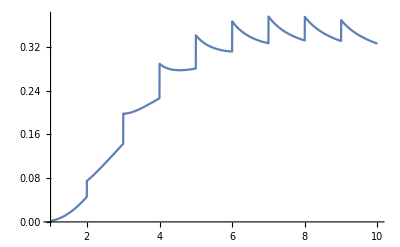

```mathematica
Plot[sigthresh[k,k,10^(-3)],{k,1,10}]
```

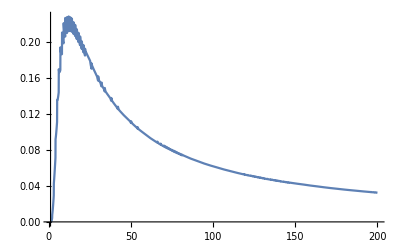

```mathematica
Plot[sigthresh[k,k,10^(-5)],{k,1,200}]
```

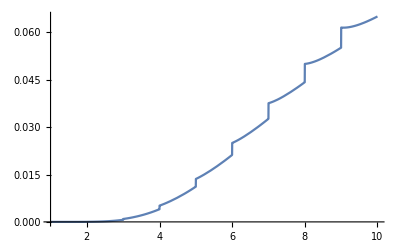

```mathematica
Plot[sigthresh[k,k,10^(-10)],{k,1,10}]
```

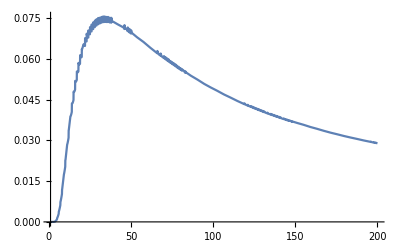

```mathematica
Plot[sigthresh[k,k,10^(-15)],{k,1,200}]
```

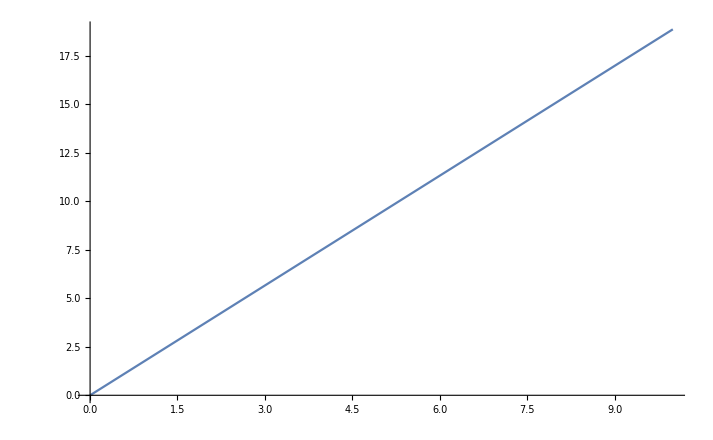

```mathematica
Plot[sigthresh[1,1,ϵ],{ϵ,0,10}]
```

Why did we do this last step? Because! sigthresh ~ eps^(1/k), so for k=1 we expect it to look linear. The nice thing is
that we get reasonable values for sigthresh.

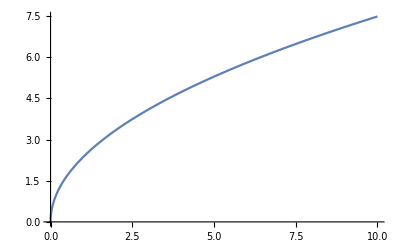

```mathematica
Plot[sigthresh[2,2,ϵ],{ϵ,0,10}]
```

As a sanity check,

```mathematica
sigthresh[200,200,10^(-120)]//N
```

0.00867722

So this is pretty reasonable for Bousso-Polchinski. But what if we had few moduli?

```mathematica
sigthresh[10,10,10^(-120)]//N
```

7.17522×10^-13

```mathematica
Table[sigthresh[k,k,10^(-10)],{k,200,500,20}]//N
```

{0.0307879,0.0282571,0.0261081,0.0242613,0.0226573,0.0212514,0.0200092,0.0189037,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
sigthresh[2,2,10^(-2)]//N
```

0.236546

Some checks against the Python code sigthresh.py

```mathematica
Table[sigthresh[k,k,10^-ϵ],{k,10,100,10},{ϵ,10,100,10}]//N//MatrixForm
```

(0.0717522 | 0.00717522 | 0.000717522 | 0.0000717522 | 7.17522×10^-6 | 7.17522×10^-7 | 7.17522×10^-8 | 7.17522×10^-9 | 7.17522×10^-10 | 7.17522×10^-11
0.1135 | 0.035892 | 0.01135 | 0.0035892 | 0.001135 | 0.00035892 | 0.0001135 | 0.000035892 | 0.00001135 | 3.5892×10^-6
0.11027 | 0.0511827 | 0.0237569 | 0.011027 | 0.00511827 | 0.00237569 | 0.0011027 | 0.000511827 | 0.000237569 | 0.00011027
0.0996146 | 0.0560174 | 0.0315009 | 0.0177143 | 0.00996146 | 0.00560174 | 0.00315009 | 0.00177143 | 0.000996146 | 0.000560174
0.0890169 | 0.0561659 | 0.0354383 | 0.02236 | 0.0141082 | 0.00890169 | 0.00561659 | 0.00354383 | 0.002236 | 0.00141082
0.0798192 | 0.0543802 | 0.0370488 | 0.0252411 | 0.0171965 | 0.0117159 | 0.00798192 | 0.00543802 | 0.00370488 | 0.00252411
0.0720701 | 0.0518678 | 0.0373285 | 0.0268648 | 0.0193342 | 0.0139146 | 0.0100141 | 0.00720701 | 0.00518678 | 0.00373285
0.0655578 | 0.0491614 | 0.0368659 | 0.0276455 | 0.0207312 | 0.0155462 | 0.011658 | 0.00874227 | 0.00655578 | 0.00491614
0.0600522 | 0.0464962 | 0.0360003 | 0.0278738 | 0.0215816 | 0.0167099 | 0.0129379 | 0.0100173 | 0.00775604 | 0.00600522
0.0553575 | 0.043972 | 0.0349282 | 0.0277445 | 0.0220382 | 0.0175056 | 0.0139052 | 0.0110453 | 0.00877357 | 0.0069691)

```mathematica
test=Table[sigthresh[k,k,10^-ϵ],{k,10,100,10},{ϵ,10,100,10}]//N
```

{{0.0717522,0.00717522,0.000717522,0.0000717522,7.17522×10^-6,7.17522×10^-7,7.17522×10^-8,7.17522×10^-9,7.17522×10^-10,7.17522×10^-11},{0.1135,0.035892,0.01135,0.0035892,0.001135,0.00035892,0.0001135,0.000035892,0.00001135,3.5892×10^-6},{0.11027,0.0511827,0.0237569,0.011027,0.00511827,0.00237569,0.0011027,0.000511827,0.000237569,0.00011027},{0.0996146,0.0560174,0.0315009,0.0177143,0.00996146,0.00560174,0.00315009,0.00177143,0.000996146,0.000560174},{0.0890169,0.0561659,0.0354383,0.02236,0.0141082,0.00890169,0.00561659,0.00354383,0.002236,0.00141082},{0.0798192,0.0543802,0.0370488,0.0252411,0.0171965,0.0117159,0.00798192,0.00543802,0.00370488,0.00252411},{0.0720701,0.0518678,0.0373285,0.0268648,0.0193342,0.0139146,0.0100141,0.00720701,0.00518678,0.00373285},{0.0655578,0.0491614,0.0368659,0.0276455,0.0207312,0.0155462,0.011658,0.00874227,0.00655578,0.00491614},{0.0600522,0.0464962,0.0360003,0.0278738,0.0215816,0.0167099,0.0129379,0.0100173,0.00775604,0.00600522},{0.0553575,0.043972,0.0349282,0.0277445,0.0220382,0.0175056,0.0139052,0.0110453,0.00877357,0.0069691}}

```mathematica
For[i=1,i≤Length[test],i++,
For[j=1,j≤Length[test[[i]]],j++, Print[{i-1,j-1,test[[i]][[j]]}]]
];
```

{0,0,0.0717522}

{0,1,0.00717522}

{0,2,0.000717522}

{0,3,0.0000717522}

{0,4,7.17522×10^-6}

{0,5,7.17522×10^-7}

{0,6,7.17522×10^-8}

{0,7,7.17522×10^-9}

{0,8,7.17522×10^-10}

{0,9,7.17522×10^-11}

{1,0,0.1135}

{1,1,0.035892}

{1,2,0.01135}

{1,3,0.0035892}

{1,4,0.001135}

{1,5,0.00035892}

{1,6,0.0001135}

{1,7,0.000035892}

{1,8,0.00001135}

{1,9,3.5892×10^-6}

{2,0,0.11027}

{2,1,0.0511827}

{2,2,0.0237569}

{2,3,0.011027}

{2,4,0.00511827}

{2,5,0.00237569}

{2,6,0.0011027}

{2,7,0.000511827}

{2,8,0.000237569}

{2,9,0.00011027}

{3,0,0.0996146}

{3,1,0.0560174}

{3,2,0.0315009}

{3,3,0.0177143}

{3,4,0.00996146}

{3,5,0.00560174}

{3,6,0.00315009}

{3,7,0.00177143}

{3,8,0.000996146}

{3,9,0.000560174}

{4,0,0.0890169}

{4,1,0.0561659}

{4,2,0.0354383}

{4,3,0.02236}

{4,4,0.0141082}

{4,5,0.00890169}

{4,6,0.00561659}

{4,7,0.00354383}

{4,8,0.002236}

{4,9,0.00141082}

{5,0,0.0798192}

{5,1,0.0543802}

{5,2,0.0370488}

{5,3,0.0252411}

{5,4,0.0171965}

{5,5,0.0117159}

{5,6,0.00798192}

{5,7,0.00543802}

{5,8,0.00370488}

{5,9,0.00252411}

{6,0,0.0720701}

{6,1,0.0518678}

{6,2,0.0373285}

{6,3,0.0268648}

{6,4,0.0193342}

{6,5,0.0139146}

{6,6,0.0100141}

{6,7,0.00720701}

{6,8,0.00518678}

{6,9,0.00373285}

{7,0,0.0655578}

{7,1,0.0491614}

{7,2,0.0368659}

{7,3,0.0276455}

{7,4,0.0207312}

{7,5,0.0155462}

{7,6,0.011658}

{7,7,0.00874227}

{7,8,0.00655578}

{7,9,0.00491614}

{8,0,0.0600522}

{8,1,0.0464962}

{8,2,0.0360003}

{8,3,0.0278738}

{8,4,0.0215816}

{8,5,0.0167099}

{8,6,0.0129379}

{8,7,0.0100173}

{8,8,0.00775604}

{8,9,0.00600522}

{9,0,0.0553575}

{9,1,0.043972}

{9,2,0.0349282}

{9,3,0.0277445}

{9,4,0.0220382}

{9,5,0.0175056}

{9,6,0.0139052}

{9,7,0.0110453}

{9,8,0.00877357}

{9,9,0.0069691}

By the method of eyeball, this compares nicely to the output of sigthresh.py, so we’ll assume we’re good to go! Time to copy it over to our friend cc.py.